```mathematica
FullSimplify[√(B0^2+((α0^2+1)^2)/(η^2 B0^2)+(2 α0^2-2)/η)]
```

√(-4.+B0^2+4. α0^2+(4. (1+α0^2)^2)/B0^2)

```mathematica
Expand[(B0+(α0^2+1)/(η B0)-2)^2]
```

8.+4./B0^2-8./B0-4 B0+B0^2+4. α0^2+(8. α0^2)/B0^2-(8. α0^2)/B0+(4. α0^4)/B0^2

```mathematica
Solve[a x+y==7&&b x-y==1,{x,y}]
```

{{x→8/(a+b),y→-(a-7 b)/(a+b)}}

```mathematica
sol=Solve[Bs+(L-Ss)^2/Bs==(1/2-1/(2 η))Cos[2 √η L]+1/2+1/(2 η)&&(L-Ss)/Bs==1/2 (1/η-√η) Sin[2 √η L],{Ss, Bs}];
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

```mathematica
FullSimplify[Bs/.sol]
```

{(2.60712×10^16-8.69041×10^15 Cos[1.41421 L])/(2.10125×10^16-3.63166×10^15 Cos[2.82843 L])}

```mathematica
FullSimplify[Ss/.sol]
```

{(2.10125×10^16 L-3.63166×10^15 L Cos[2.82843 L]-1.68537×10^16 Sin[1.41421 L]+2.80894×10^15 Sin[2.82843 L])/(2.10125×10^16-3.63166×10^15 Cos[2.82843 L])}

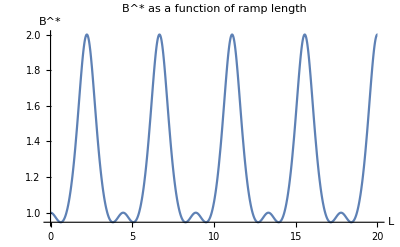

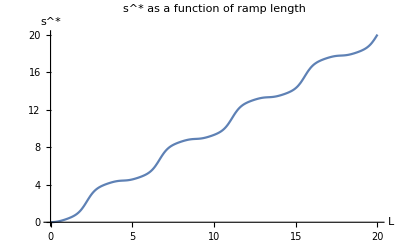

```mathematica
η=0.5;
Plot[(2 η (1+η+(-1+η) Cos[2 L √η]))/(4 η^2+(-1+η^(3/2))^2 Sin[2 L √η]^2),{L,0,20},AxesLabel->{"L","B^*"},PlotLabel->"B^* as a function of ramp length"]
Plot[(8 L η^2+2 (-1+η^(3/2)) Sin[2 L √η] (1+η+L (-1+η^(3/2)) Sin[2 L √η])+Sin[4 L √η]+(-1+(-1+η) √η) η Sin[4 L √η])/(2 (4 η^2+(-1+η^(3/2))^2 Sin[2 L √η]^2)),{L,0,20},AxesLabel->{"L","s^*"},PlotLabel->"s^* as a function of ramp length"]
```

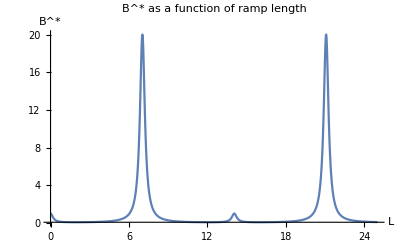

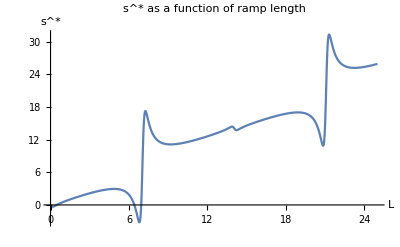

```mathematica
η=0.05;
Plot[(2 η (1+η+(-1+η) Cos[2 L √η]))/(4 η^2+(-1+η^(3/2))^2 Sin[2 L √η]^2),{L,0,25},PlotRange->Full,AxesLabel->{"L","B^*"},PlotLabel->"B^* as a function of ramp length"]
Plot[(8 L η^2+2 (-1+η^(3/2)) Sin[2 L √η] (1+η+L (-1+η^(3/2)) Sin[2 L √η])+Sin[4 L √η]+(-1+(-1+η) √η) η Sin[4 L √η])/(2 (4 η^2+(-1+η^(3/2))^2 Sin[2 L √η]^2)),{L,0,25},AxesLabel->{"L","s^*"},PlotLabel->"s^* as a function of ramp length"]
```